```mathematica
Quit
```

```mathematica
(*Define Sinai Billiard Region)
```

```mathematica
Ω=ImplicitRegion[x^2+1.05y^2≥1,{{x,-2,2},{y,-2,2}}];
RegionPlot[Ω]
```

-Graphics-

```mathematica
(*Generate eigenvalues of the Sinai Billiard problem. Maximally can go to 872th eigenvalue due to numerical limitations)
```

```mathematica
SinaiList=NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Ω,872];
```

```mathematica
SinaiDeltaList200=SinaiList[[2;;201]]-SinaiList[[1;;200]];
```

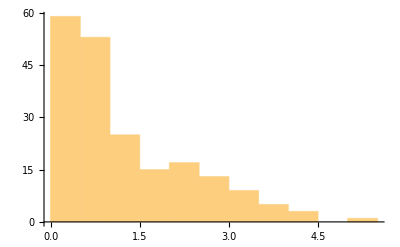

```mathematica
Histogram[SinaiDeltaList200]
```

```mathematica
SinaiDeltaList400=SinaiList[[2;;401]]-SinaiList[[1;;400]];
```

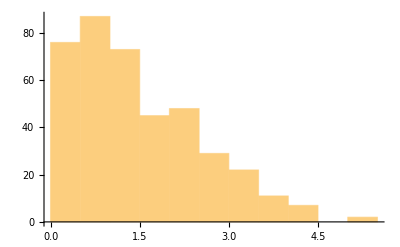

```mathematica
Histogram[SinaiDeltaList400]
```

```mathematica
SinaiDeltaList850=SinaiList[[2;;851]]-SinaiList[[1;;850]];
```

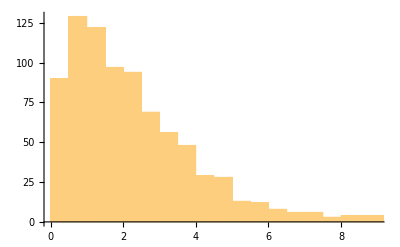

```mathematica
Histogram[SinaiDeltaList850]
```

```mathematica
(*We start to see trends of level repulsion. But not clean enough. TOO FEW DATAPOINTS!!)
```

```mathematica
(**Aside on Weyl's Law)
```

```mathematica
(*The spectrum should fluctuate around the Weyl's law prediction below where L is the perimeter of the boundary region and A is the area of the billiard table)
```

```mathematica
Eweyl[n_,A_,L_]=(4*Pi*n)/A+(Sqrt[4*Pi]*L)/A Sqrt[n]
```

(2 L √n √π)/A+(4 n π)/A

```mathematica
A=16-Pi
```

16-π

```mathematica
L =16+2*Pi
```

16+2 π

```mathematica
Elist=Table[Eweyl[n,A,L],{n,1,872}];
```

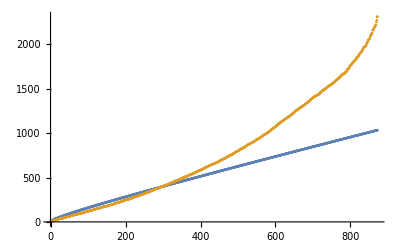

```mathematica
ListPlot[{Elist,SinaiList}]
```

```mathematica
(*We see large deviations after about the 350th eigenvalue. What is going on????)
```

```mathematica
(**To be safe let's now restrict to eigenvalues below 350)
```

```mathematica
(*We don't have enough datapoints. Let's try to get around this problem by adding some fictitious disorder in the shape of the billiard table)
```

```mathematica
(*First draw some random numbers near 1)
```

```mathematica
ParametersX=RandomReal[{0.8,1.2},30];
```

```mathematica
ParametersY=RandomReal[{0.8,1.2},30];
```

```mathematica
(*Use these numbers to stretch the circular wall into elliptic walls randomly)
```

```mathematica
Ωtab=Table[ImplicitRegion[ParametersX[[p]]*x^2+ParametersY[[p]]*y^2≥1,{{x,-2,2},{y,-2,2}}],{p,1,Length[ParametersX]}];
```

```mathematica
(*Define a function that takes a spectrum, and computes the spacing statistics for a subspectrum from Elow0 to Eup0)
```

```mathematica
delta[list0_,Elow0_,Eup0_]:=Module[{list=list0,Elow=Elow0,Eup=Eup0,c},c=list[[Elow+1;;Eup+1]]-list[[Elow;;Eup]];
c];
```

```mathematica
(*Compute delta for high energy part of the spectrum. Expect WD)
```

```mathematica
SinaiDeltaHighEtab=Table[delta[NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Ωtab[[i]],350]，150，349],{i,1,Length[ParametersX]}];
```

```mathematica
SinaiDeltaHighEAggregated=SinaiDeltaHighEtab//Flatten;
```

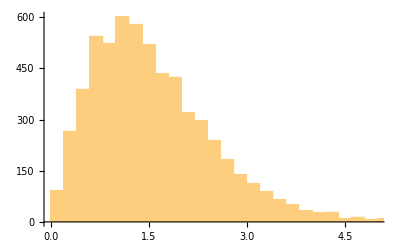

```mathematica
Histogram[SinaiDeltaAggregated,50]
```

```mathematica
(*It worked! Now let's do the same thing for the low energy part of the spectrum)
```

```mathematica
SinaiDeltaLowEtab=Table[delta[NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Ωtab[[i]],350],1,100],{i,1,Length[ParametersX]}];
```

```mathematica
SinaiDeltaLowEAggregated=SinaiDeltaLowEtab//Flatten;
```

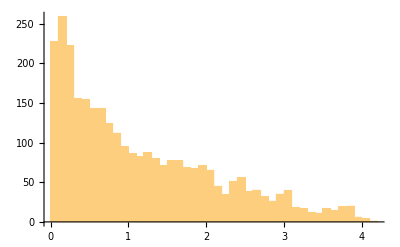

```mathematica
Histogram[SinaiDeltaLowEAggregated,50]
```

```mathematica
(*No WD anymore!!)
```

```mathematica
SinaiDeltaMedEtab=Table[delta[NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Ωtab[[i]],350],50,100],{i,1,Length[ParametersX]}];
```

```mathematica
SinaiDeltaMedEAggregated=SinaiDeltaMedEtab//Flatten;
```

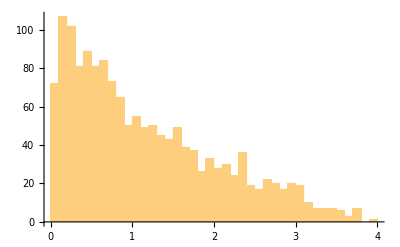

```mathematica
Histogram[SinaiDeltaMedEAggregated,50]
```

```mathematica
(***SFF***)
```

```mathematica
K[t_,list_]:=Conjugate[Total[Exp[I*list*t]]]*Total[Exp[I*list*t]]//N
```

```mathematica
Ktab=Table[K[t,SinaiList[[351;;650]]],{t,0,150,0.01}];
```

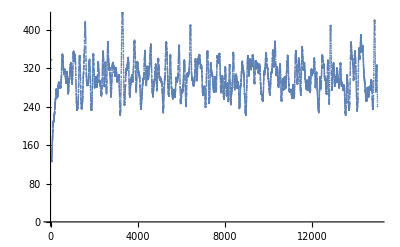

```mathematica
ListPlot[Re[GaussianFilter[Ktab,50]]]
```